```mathematica
allK={};
allL={};
allGDP={};
```

```mathematica
data=Import["C:\Users\Valeria\Downloads\usa1936-50.xls"];
```

```mathematica
neededData=FlattenAt[data,2][[1]][[3;;]];
For[i=1,i<=Length[neededData],i++,AppendTo[allGDP,neededData[[i]][[2]]];AppendTo[allK,neededData[[i]][[3]]];AppendTo[allL,neededData[[i]][[4]]]];
```

```mathematica
allK=Log@allK;
allL=Log@allL;
allGDP=Log@allGDP;
```

```mathematica
(*случай α+β не обязательно == 1*)
```

```mathematica
matr={{Length@neededData,Total@allK, Total@allL},
	   {Total@allK,Total@( allK^2),Total@(allK*allL)},
	   {Total@allL,Total@(allK*allL),Total@(allL^2)}};
matr//MatrixForm
```

(15 | 186.803 | 171.041
186.803 | 2326.49 | 2130.22
171.041 | 2130.22 | 1950.58)

```mathematica
vec={Total@allGDP, Total@(allGDP*allK),Total@(allGDP*allL)};
vec//MatrixForm
```

(175.592
2187.02
2002.66)

```mathematica
res=LinearSolve[matr,vec];
res//MatrixForm
```

(-9.65104
0.358166
1.48182)

```mathematica
"A = "0.0000643588692546109"\nα = "0.3581662946206474"\nβ = "1.4818203831444123
```

A = 0.0000643589
α = 0.358166
β = 1.48182

```mathematica
A=Exp[res[[1]]];
α=res[[2]];
β=res[[3]];
```

```mathematica
f[k_,l_]:=A*k^α*l^β
modelPoints={};
historicalPoints={};
For[i=1,i<=Length[neededData],i++,AppendTo[modelPoints,{neededData[[i]][[1]],f[neededData[[i]][[3]],neededData[[i]][[4]]]}]]
For[i=1,i<=Length[neededData],i++,AppendTo[historicalPoints,{neededData[[i]][[1]],neededData[[i]][[2]]}]]
```

```mathematica
ListLinePlot[{historicalPoints, modelPoints},PlotStyle->{Blue,Red},PlotLabels->{"historicalPoints","modelPoints"},PlotRange->{70000,160000}]
```

-Graphics-

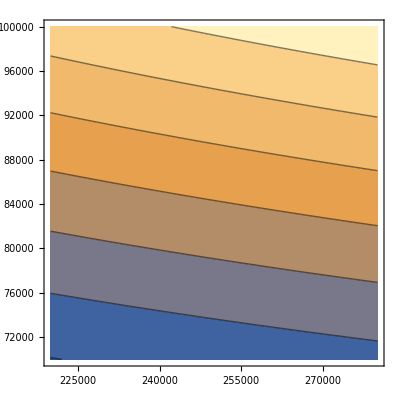

```mathematica
ContourPlot[f[k,l],{k,220000,280000},{l,70000,100000}]
```

```mathematica
(*случай α+β == 1*)
```

```mathematica
matr={{Length@neededData, Total@(allK-allL)},
               {Total@(allK-allL), Total@(((allK-allL))^2)}};
matr//MatrixForm
```

(15 | 15.7627
15.7627 | 16.6378)

```mathematica
vec={Total@(allGDP-allL),
Total@((allGDP-allL)*(allK-allL))};
vec//MatrixForm
```

(4.55193
4.72654)

```mathematica
res=LinearSolve[matr, vec];
res//MatrixForm
Print["A = ",Exp[res[[1]]],"\nα = ",res[[2]]]
```

(1.11567
-0.772906)

A = 3.05161
α = -0.772906

```mathematica
A=Exp[res[[1]]];
α=res[[2]];
```

```mathematica
f[k_,l_]:=A*k^α*l^(1-α)
historicalPoints={};
modelPoints={};
For[i=1,i<=Length[neededData],i++,AppendTo[modelPoints,{neededData[[i]][[1]],f[neededData[[i]][[3]],neededData[[i]][[4]]]}]]
For[i=1,i<=Length[neededData],i++,AppendTo[historicalPoints,{neededData[[i]][[1]],neededData[[i]][[2]]}]]
```

```mathematica
ListLinePlot[{historicalPoints, modelPoints},PlotLabels->{"historicalPoints","modelPoints"},PlotStyle->{Blue,Red}]
```

-Graphics-

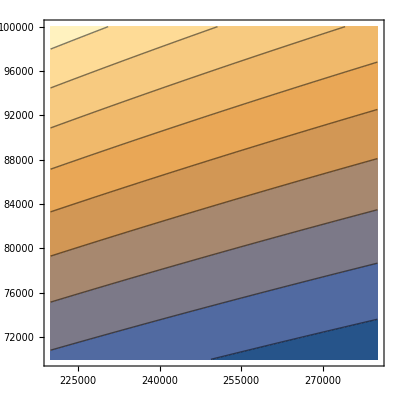

```mathematica
ContourPlot[f[k,l],{k,220000,280000},{l,70000,100000}]
```